```mathematica
pPrime = Simplify[-((p+ρ0)(m + 4π r^3(p+2/3 pΛ)))/(r(r-2 m +8/3 π r^3 pΛ))/. m -> 4/3 π r^3 ρ0]
```

(4 π r (p+ρ0) (3 p+2 pΛ+ρ0))/(-3+8 π r^2 (-pΛ+ρ0))

```mathematica
LHS = Simplify[Integrate[1/((p+ρ0) (3 p+2 pΛ+ρ0)),p]]
```

(Log[3 (p+ρ0)]-Log[3 p+2 pΛ+ρ0])/(2 (pΛ-ρ0))

```mathematica
RHS = Simplify[Integrate[-(4 π r)/(3+8 π r^2 (pΛ-ρ0)),r]]
```

-Log[3+8 π r^2 (pΛ-ρ0)]/(4 (pΛ-ρ0))

```mathematica
FullSimplify[Solve[Log[(3 p +2 pΛ +ρ0)/(p+ρ0)] == 1/2 Log[1-8/3 π r^2(ρ0-pΛ)] + Log[(3 pc +2 pΛ +ρ0)/(pc+ρ0)],p]]
```

{{p→ConditionalExpression[-(-2 pΛ-ρ0+(√(1+8/3 π r^2 (pΛ-ρ0)) ρ0 (3 pc+2 pΛ+ρ0))/(pc+ρ0))/(-3+(√(1+8/3 π r^2 (pΛ-ρ0)) (3 pc+2 pΛ+ρ0))/(pc+ρ0)),-2 π<Arg[1+8/3 π r^2 (pΛ-ρ0)]+2 Arg[1+(2 (pc+pΛ))/(pc+ρ0)]≤2 π]}}

```mathematica
FullSimplify[Solve[Simplify[Log[(3 p +2 pΛ +ρ0)/(p+ρ0)] == 1/2 Log[1-8/3 π r^2(ρ0-pΛ)] + Log[(3 pc +2 pΛ +ρ0)/(pc+ρ0)]/.{ r-> R,p-> 0}],pc]]
```

{{pc→ConditionalExpression[((-3+√3 √(3+8 π R^2 (pΛ-ρ0))) (2 pΛ+ρ0))/(3 (1-3 √(1+8/3 π R^2 (pΛ-ρ0))+(2 pΛ)/ρ0)),-2 π≤Arg[1+8/3 π R^2 (pΛ-ρ0)]-2 Arg[1+(2 pΛ)/ρ0]<2 π]}}

```mathematica
FullSimplify[-(-2 pΛ-ρ0+(√(1+8/3 π r^2 (pΛ-ρ0)) ρ0 (3 pc+2 pΛ+ρ0))/(pc+ρ0))/(-3+(√(1+8/3 π r^2 (pΛ-ρ0)) (3 pc+2 pΛ+ρ0))/(pc+ρ0))/. pc-> ((-3+√3 √(3+8 π R^2 (pΛ-ρ0))) (2 pΛ+ρ0))/(3 (1-3 √(1+8/3 π R^2 (pΛ-ρ0))+(2 pΛ)/ρ0))]
```

-((√(3+8 π r^2 (pΛ-ρ0))-√(3+8 π R^2 (pΛ-ρ0))) ρ0 (2 pΛ+ρ0))/(2 pΛ √(3+8 π r^2 (pΛ-ρ0))+(√(3+8 π r^2 (pΛ-ρ0))-3 √(3+8 π R^2 (pΛ-ρ0))) ρ0)

```mathematica
FullSimplify[Solve[Simplify[Log[(3 p +2 pΛ +ρ0)/(p+ρ0)] == 1/2 Log[1-8/3 π r^2(ρ0-pΛ)] + Log[(3 pc +2 pΛ +ρ0)/(pc+ρ0)]/.{r-> R, p-> 0}],R]]
```

{{R→ConditionalExpression[-(√(3/(2 π)) √((pc (pΛ-ρ0) (pc pΛ+2 (pc+pΛ) ρ0+ρ0^2))/(ρ0^2 (3 pc+2 pΛ+ρ0)^2)))/(√(pΛ-ρ0)),-π<2 (Arg[1+(2 pΛ)/ρ0]-Arg[1+(2 (pc+pΛ))/(pc+ρ0)])≤π]},{R→ConditionalExpression[(√(3/(2 π)) √((pc (pΛ-ρ0) (pc pΛ+2 (pc+pΛ) ρ0+ρ0^2))/(ρ0^2 (3 pc+2 pΛ+ρ0)^2)))/(√(pΛ-ρ0)),-π<2 (Arg[1+(2 pΛ)/ρ0]-Arg[1+(2 (pc+pΛ))/(pc+ρ0)])≤π]}}

```mathematica
R = √(3/(2 π)) √((pc  (pc pΛ+2 (pc+pΛ) ρ0+ρ0^2))/(ρ0^2 (3 pc+2 pΛ+ρ0)^2))
```

√(3/(2 π)) √((pc (pc pΛ+2 (pc+pΛ) ρ0+ρ0^2))/(ρ0^2 (3 pc+2 pΛ+ρ0)^2))

```mathematica
Simplify[R /. {pΛ-> ρ0}]
```

√(pc/(2 pc π ρ0+2 π ρ0^2))

```mathematica
Solve[Simplify[2 pΛ √(3+8 π r^2 (pΛ-ρ0))+(√(3+8 π r^2 (pΛ-ρ0))-3 √(3+8 π R^2 (pΛ-ρ0))) ρ0/.{ ρ0-> M 3/(4 π R^3),r-> 0}]==0,M]
```

{{M→4/3 π pΛ R^3},{M→2/9 (R-√(R^2+6 π pΛ R^4))},{M→2/9 (R+√(R^2+6 π pΛ R^4))}}

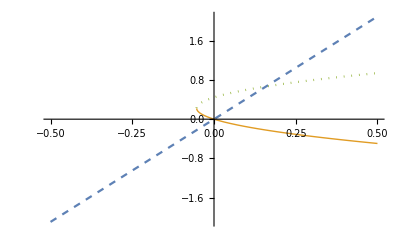

```mathematica
Plot[{4/3 π pΛ R^3/. {R-> 1},2/9 (R-√(R^2+6 π pΛ R^4))/. {R-> 1},2/9 (R+√(R^2+6 π pΛ R^4))/. {R-> 1}},{pΛ,-.5,.5},PlotStyle->{Dashed,Thick,Dotted}]
```

```mathematica
foo = Simplify[1 - 2 ((4/3 π r^3)ρ0)/r+8/3 π r^2 pΛ]
```

1/3 (3+8 π r^2 (pΛ-ρ0))

```mathematica
Solve[1+x == 1/foo,x]
```

{{x→-1+3/(3+8 π r^2 (pΛ-ρ0))}}

```mathematica
foo2 = Simplify[Integrate[Simplify[√(-(3+8 π r^2 (pΛ-ρ0))/(3+8 π r^2 (pΛ-ρ0))+3/(3+8 π r^2 (pΛ-ρ0)))],{r,0,r}]]
```

ConditionalExpression[(√(3/(2 π)))/(2 √(-pΛ+ρ0))-r/(4 √π √((r^2 (-pΛ+ρ0))/(6+16 π r^2 (pΛ-ρ0)))),Re[1/(r √(-pΛ+ρ0))]>2 √((2 π)/3)||Re[1/(r √(-pΛ+ρ0))]<-2 √((2 π)/3)||1/(r √(-pΛ+ρ0))∉Reals]

```mathematica
Simplify[foo2 /. ρ0 -> M 3/(4π R^3)]
```

ConditionalExpression[(1/(√(-(4 π pΛ)/3+M/R^3))-r/(√((r^2 (3 M-4 π pΛ R^3))/(-6 M r^2+(3+8 π pΛ r^2) R^3))))/(√2),Re[1/(r √(-pΛ+(3 M)/(4 π R^3)))]>2 √((2 π)/3)||Re[1/(r √(-pΛ+(3 M)/(4 π R^3)))]<-2 √((2 π)/3)||1/(r √(-pΛ+(3 M)/(4 π R^3)))∉Reals]

```mathematica
z = √(R^3/(2 M))1/(√(1-pΛ/ρ0))(1-√(1-8/3 π r^2(ρ0-pΛ)))
```

(√(R^3/M) (1-√(1-8/3 π r^2 (-pΛ+ρ0))))/(√2 √(1-pΛ/ρ0))

```mathematica
Limit[z, pΛ-> ρ0]
```

0

```mathematica
Simplify[z/. pΛ-> ρ0]
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression (0 √(R^3/M) ComplexInfinity)/(√2) encountered.

Indeterminate

```mathematica
Piecewise[{{√(1+r^2),{r,0,1}},{1/r,r>1}}]
```

Piecewise[{{√(1+r^2), {r,0,1}}, {1/r, r>1}, {0, True}}]

```mathematica
Plot[Piecewise[{{√(1+r^2),{r,0,1}},{1/r,r>1}}],{r,0,4}]
```

-Graphics-

```mathematica
Solve[Simplify[a-√(1+r^2)==1/r/.r-> 1],a]
```

{{a→1+√2}}

```mathematica
RevolutionPlot3D[  Piecewise[{{1+√2-√(1+r^2),r<1},{1/r,r>1}}],{r,0,4},Boxed->False,Axes->False,Ticks->None,PlotStyle->Opacity[.1],ImageSize->{500,500}]
```

-Graphics3D-

```mathematica
Plot[Piecewise[{{√(1+x^2),{x,0,1}},{1/x,{x,1,2}}}],{x,-2,2}]
```

-Graphics-